```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression,100];Length[deps3]
```

100

```mathematica
Take[deps3,5]
```

{{2,3,{3,{2,5,4,1,3},{2<->4,2<->5},{{2,3,4},{2,4,5},{1,2,5}}}},{3,6,{3,{5,3,1,4,2},{1<->5,3<->5},{{1,2,5},{1,3,5},{3,4,5}}}},{3,5,{3,{2,6,5,3,1},{2<->5,2<->6},{{1,2,5},{2,5,6},{2,3,6}}}},{3,7,{3,{5,6,2,4,1},{2<->5,5<->6},{{1,2,5},{2,5,6},{4,5,6}}}},{3,9,{3,{6,4,3,5,2},{3<->6,4<->6},{{2,3,6},{3,4,6},{4,5,6}}}}}

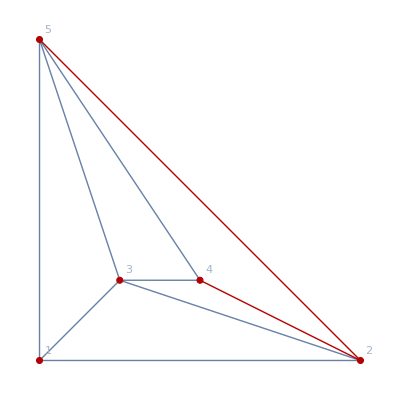
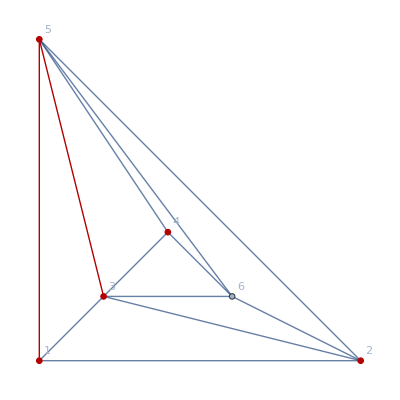
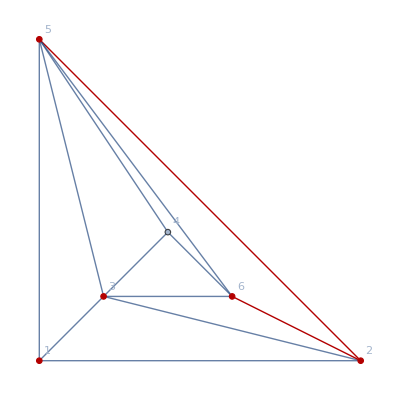
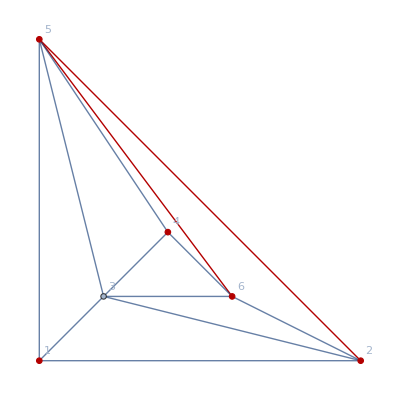
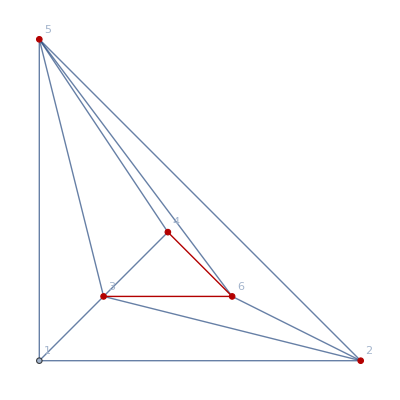

```mathematica
Map[With[
{g=ReadGrof[#[[1]]]},
Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding", GraphHighlight->Join[#[[3,2]],#[[3,3]]]]]&,
Take[deps3,5]
]
```

```mathematica
Subsets[Range[5],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

```mathematica
GenGraphs[g_,vertices_]:=Block[
{couples=Map[#[[1]]<->#[[2]]&,},
couples=DeleteDuplicates[Map[Sort[#]&,couples]];
couples=Map[vertices[[#[[1]]]]<->vertices[[#[[2]]]]&,couples];
Map[EdgeAdd[g,#]&,couples]
]
```

```mathematica
GenDoubleGraphs[g_,vertices_]:=Block[
{edges=Table[{
vertices[[i]]<->
vertices[[Mod[i+2,5]+1]]
,
vertices[[i]]<->
vertices[[Mod[i+3,5]+1]]
},{{i,j},Subsets[Range[5],2]}]},
Print[edges];
Map[EdgeAdd[g,#]&,edges]
]
```

```mathematica
111
```

```mathematica
{{2,3,6},{3,4,6},{4,5,6}}
```

EdgeAdd::inv: The argument {(2 <-> 2)[1], (2 <-> 2)[1], (2 <-> 2)[4], (2 <-> 2)[5]} in EdgeAdd[Graph[<5>, <7>], {(2 <-> 2)[1], (2 <-> 2)[1], (2 <-> 2)[4], (2 <-> 2)[5]}] is not a valid "edge".

EdgeAdd::inv: The argument {(2 <-> 5)[1], (2 <-> 5)[2], (2 <-> 5)[2], (2 <-> 5)[5]} in EdgeAdd[Graph[<5>, <7>], {(2 <-> 5)[1], (2 <-> 5)[2], (2 <-> 5)[2], (2 <-> 5)[5]}] is not a valid "edge".

EdgeAdd::inv: The argument {(2 <-> 5)[1], (2 <-> 5)[2], (2 <-> 5)[3], (2 <-> 5)[3]} in EdgeAdd[Graph[<5>, <7>], {(2 <-> 5)[1], (2 <-> 5)[2], (2 <-> 5)[3], (2 <-> 5)[3]}] is not a valid "edge".

General::stop: Further output of EdgeAdd :: inv will be suppressed during this calculation.

ChromaticPolynomial::graph: A graph object is expected at position 1 in EdgeAdd[GraphicsBox[NamespaceBox[.

General::stop: Further output of ChromaticPolynomial :: graph will be suppressed during this calculation.

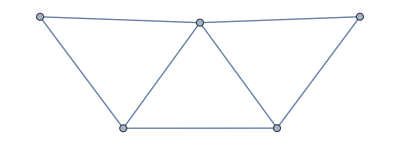
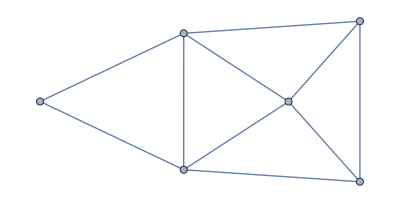
{{4,1,{4,4,3,4,4,4,2,4,2,4},{1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(2<->2)[1],(2<->2)[1],(2<->2)[4],(2<->2)[5]}],4],1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(2<->5)[1],(2<->5)[2],(2<->5)[2],(2<->5)[5]}],4],1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(2<->5)[1],(2<->5)[2],(2<->5)[3],(2<->5)[3]}],4],1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(5<->4)[2],(5<->4)[3],(5<->4)[4],(5<->4)[4]}],4],1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(4<->1)[3],(4<->1)[4],(4<->1)[5],(4<->1)[5]}],4]}},{6,4,{6,6,5,6,6,6,2,6,5,2},{1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(5<->5)[1],(5<->5)[1],(5<->5)[4],(5<->5)[5]}],4],1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(5<->3)[1],(5<->3)[2],(5<->3)[2],(5<->3)[5]}],4],1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(5<->3)[1],(5<->3)[2],(5<->3)[3],(5<->3)[3]}],4],1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(3<->1)[2],(3<->1)[3],(3<->1)[4],(3<->1)[4]}],4],1/24 ChromaticPolynomial[EdgeAdd[-Graphics-,{(1<->4)[3],(1<->4)[4],(1<->4)[5],(1<->4)[5]}],4]}}}

```mathematica
Map[With[
{g=EdgeDelete[ReadGrof[#[[1]]],#[[3,3]]]},
Join[
{ChromaticPolynomial[g,4]/24,
ChromaticPolynomial[ReadGrof[#[[2]]],4]/24
},
{
Map[ChromaticPolynomial[#,4]/24&,GenGraphs[g,#[[3,2]]]]
},
{
Map[ChromaticPolynomial[#,4]/24&,GenDoubleGraphs[g,#[[3,2]]]]
}]
]&,
Take[deps3,2]
]
```

```mathematica
Graph[ReadGrof[3],GraphHighlight->{6,4,3,5,2,3<->6,4<->6}, VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

-Graphics-

```mathematica
EdgeList[ReadGrof[2]]
```

{1<->2,1<->3,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

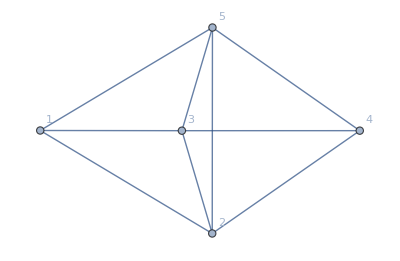

```mathematica
Graph[ReadGrof[2], VertexLabels->"Name"]
```

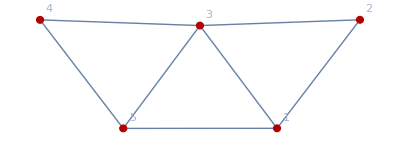

```mathematica
Graph[EdgeDelete[ReadGrof[2],{2<->4,2<->5}],GraphHighlight->{2,5,4,1,3}, VertexLabels->"Name"]
```

{{2<->1,2<->3},{5<->3,5<->2},{4<->2,4<->5},{1<->5,1<->4},{3<->4,3<->1}}

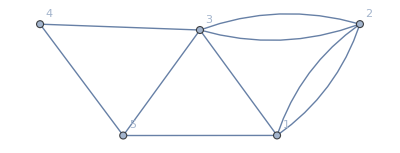
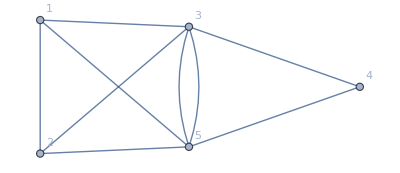
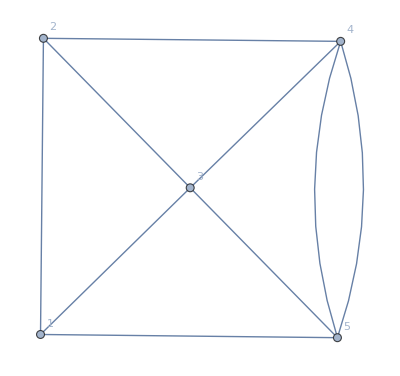
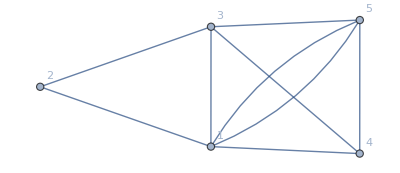
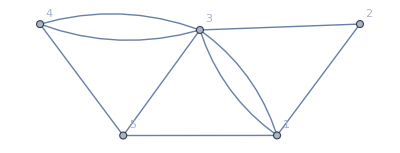

```mathematica
With[
{g=EdgeDelete[ReadGrof[2],{2<->4,2<->5}]},
Map[Graph[#, VertexLabels->"Name"]&,GenDoubleGraphs[g,{2,5,4,1,3}]]
]
```

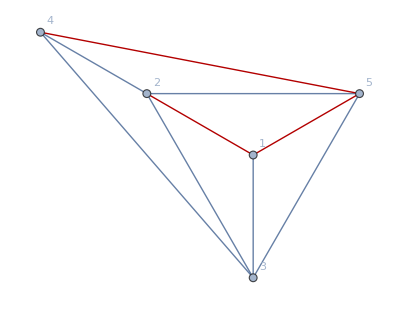

```mathematica
Graph[ReadGrof[2],GraphHighlight->{1<->5,4<->5,4<->6,6<->2,2<->1}, VertexLabels->"Name", GraphLayout->"RadialDrawing"]
```